This relates to the wave equation considered with *boundary conditions*.  
The region is [0,1] x [0, T], where T is irrational.  The BCs are u(x, 0) = u(0, t) = u(1,t) = 0, and u(x, T) = g(x), for some given function.  The Fourier Sine Series coefficients of g are an.

```mathematica
nMax  = 200;
an = Table[-(1+1(-1)^n)/n^2, {n, 1, nMax}];
```

```mathematica
T = 1/Sqrt[2]
T = (Sqrt[5]-1.)/2
```

1/(√2)

0.618034

```mathematica
denom =Table[N[Sin[n Pi T]], {n, 1, nMax}];
```

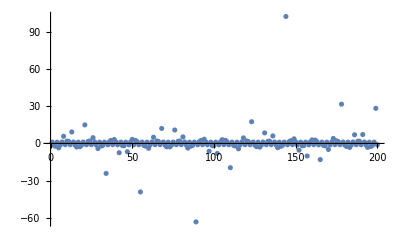

```mathematica
ListPlot[1/denom, PlotRange -> All]
```

Don' t plot the 3D solution if nMax it too big.

```mathematica
nMaxPlot = 50;
If[nMax < nMaxPlot, Print["!!"]];
u[x_, t_] := Sum[an[[n]] Sin[n Pi x] Sin[n Pi t]/denom_[[n]], {n, 1, nMaxPlot}]
Plot3D[u[x, t], {x, 0, 1}, {t, 0, T}, AxesLabel ->{x, t}, BoxRatios ->{1, T, .5}]
```

-Graphics3D-

```mathematica
(*Plot3D[u[x, t], {x, 0, 1}, {t, 0, H}, AxesLabel ->{x, t}, BoxRatios ->{1, H, .5}]*)
```

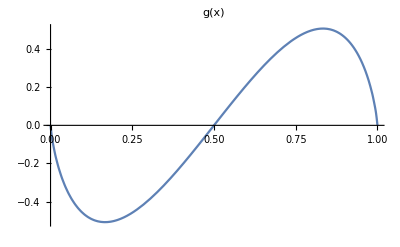

```mathematica
Plot[Sum[an_[[n]] Sin[n Pi x], {n, 1, nMax}], {x, 0, 1}, PlotLabel -> g[x]]
```

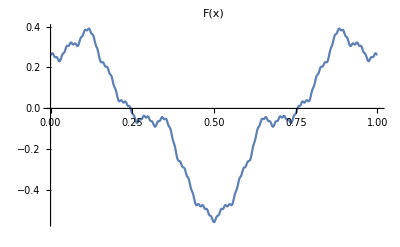

```mathematica
Plot[.5Sum[an_[[n]] Cos[n Pi x]/denom_[[n]], {n, 1, nMax}], {x, 0, 1}, PlotLabel -> F[x]]
```